```mathematica
(*Old notebook is getting highly cluttered, lets make a nice pretty one here*)
```

```mathematica
(*Plot minimal surface configs, find relation between strip width and depth*)
```

```mathematica
xa[k_]:=Quiet[NIntegrate[(k^3*Sqrt[1+y^4])/(y^2*Sqrt[y^6-k^6]),{y,k,yy}]]
```

```mathematica
xavsuatb1={};
xavsuatb2={};
xavsuatb4={};
With[{k=1},For[i=0,i<=3.5,i+=0.01,yy=k*10^i;
xa1=xa[k];
AppendTo[xavsuatb1,{yy,xa1}];
]];
With[{k=0.25},For[i=0,i<=3.25,i+=0.01,yy=k*10^i;
xa2=xa[k];
AppendTo[xavsuatb2,{yy,xa2}];
]];
With[{k=4},For[i=0,i<=3,i+=0.01,yy=k*10^i;
xa4=xa[k];
AppendTo[xavsuatb4,{yy,xa4}];
]];
xavsuatb1v2=Join[Reverse[xavsuatb1],Transpose[{xavsuatb1[[All,1]],-xavsuatb1[[All,2]]}]];
xavsuatb2v2=Join[Reverse[xavsuatb2],Transpose[{xavsuatb2[[All,1]],-xavsuatb2[[All,2]]}]];
xavsuatb4v2=Join[Reverse[xavsuatb4],Transpose[{xavsuatb4[[All,1]],-xavsuatb4[[All,2]]}]];
```

```mathematica
(*Begin SYM code*)
```

```mathematica
xvsu[uc_,uh_]:=Module[{xvsutb={},xvsutb2={}},
For[i=0,i<=3,i+=0.01,
uu=uc*10^i;
x=Quiet[NIntegrate[u^3/Sqrt[(u^6-uc^6)(u^4-uh^4)],{u,uc,uu}]];
AppendTo[xvsutb,{uu,x}];
];
xvsutb2=Join[Reverse[xvsutb],Transpose[{xvsutb[[All,1]],-xvsutb[[All,2]]}]];
Return[xvsutb2];
]
```

```mathematica
xvsu10=xvsu[1,0];
xvsu0250=xvsu[0.25,0];
xvsu40=xvsu[4,0];
```

```mathematica
symxpltt0=ListLinePlot[{xvsu10,xvsu0250,xvsu40},ScalingFunctions->{"Log","SignedLog"},PlotRange->{{0,500},Automatic},Frame->True,FrameLabel->{"u_c","x"},PlotLegends->{"u_c=1","u_c=1/4","u_c=4"},PlotStyle->Dashed];
```

```mathematica
(*End SYM code*)
```

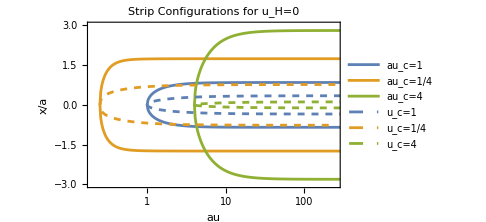

```mathematica
Show[{ListLinePlot[{xavsuatb1v2,xavsuatb2v2,xavsuatb4v2},ScalingFunctions->{"Log"}, FrameLabel->{"au","x/a"},PlotLegends->{"au_c=1","au_c=1/4","au_c=4"},Frame->True,PlotRange->{{0.2,250},{-3,3}}],symxpltt0},RotateLabel->False,PlotLabel->"Strip Configurations for u_H=0",ImageSize->Medium]
```

```mathematica
loveravsauctb={};
For[i=0.01,i≤3,i+=0.01,k=2^i-.93;
l=2*Quiet[NIntegrate[(k^3*Sqrt[1+y^4])/(y^2*Sqrt[y^6-k^6]),{y,k,Infinity}]];
AppendTo[loveravsauctb,{k,l}];
]
```

```mathematica
loveravsauctb[[FirstPosition[loveravsauctb,Min[loveravsauctb[[All,2]]]]]]
```

{{0.799074,1.61387},{0.0839595,10.2732}}

```mathematica
(*Begin SYM code*)
```

```mathematica
lvsuc[uh_]:=Module[{lvsuctb={}},
For[i=0,i<=3,i+=0.01,uc=2^i-0.93;
l=2*Quiet[NIntegrate[u^3/Sqrt[(u^6-uc^6)(u^4-uh^4)],{u,uc,Infinity}]];
If[FreeQ[l,Complex],AppendTo[lvsuctb,{uc,l}]];
];
Return[lvsuctb];
]
```

```mathematica
lvsuc0=lvsuc[0];
```

```mathematica
symlpltt0=ListLinePlot[lvsuc0,Frame->True,FrameLabel->{"u_c","l"},PlotLegends->{"SYM"},PlotStyle->Dashed];
```

```mathematica
(*End SYM code*)
```

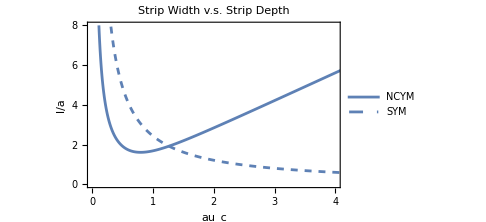

```mathematica
Show[{ListLinePlot[loveravsauctb,PlotRange->{{0,4},{0,8}},FrameLabel->{"au_c","l/a"},PlotMarkers->{None,{Automatic,Medium}},PlotLegends->{"NCYM",None},Frame->True],symlpltt0},RotateLabel->False,PlotLabel->"Strip Width v.s. Strip Depth",ImageSize->Medium]
```

```mathematica
(*While there are two Subscript[au, c] for each l/a, minimal surfaces only exist for combinations left of the minimum.*)
```

```mathematica
(*Begin finding area and entropy through RT*)
```

```mathematica
(*Calculate divergence structure*)
```

```mathematica
adiv=Integrate[u*Sqrt[1+a^4 u^4],{u,0,ub},Assumptions->{a∈Reals,u∈Reals,ub∈Reals}]
```

ConditionalExpression[1/4 (ub^2 √(1+a^4 ub^4)+ArcSinh[a^2 ub^2]/a^2), a≠0&&ub>0]

```mathematica
FullSimplify[Series[adiv,{ub,Infinity,1}]]
```

ConditionalExpression[1/4 √(a^4) ub^4+(1+Log[4 a^4 ub^4])/(8 √(a^4))+O[1/ub]^2, a≠0]

```mathematica
(*We can get rid of a few things (constants) here, will look different when we introduce dimensionless params*)
```

```mathematica
alpha=580;
spvslatb={};
For[i=0.001,i≤0.799,i+=0.01,k=i;
la=2*Quiet[NIntegrate[(k^3*Sqrt[1+y^4])/(y^2*Sqrt[y^6-k^6]),{y,k,alpha}]];
sp = 2*(Quiet[NIntegrate[y*Sqrt[(1+y^4)/(1-k^6/y^6)],{y,k,alpha}]]-((alpha)^4/4+Log[alpha]/2));
AppendTo[spvslatb,{la,sp}];]
```

```mathematica
(*Begin SYM code*)
```

```mathematica
symdelsfunct0[uh_,ub_]:=Module[{spvsltb={}},
For[uc=uh+0.0000001,uc<=3,uc+=0.025,
l=2*Quiet[NIntegrate[uc^3/Sqrt[(u^6-uc^6)(u^4-uh^4)],{u,uc,ub}]];
sp=2*(Quiet[NIntegrate[u/Sqrt[(1-(uc/u)^6)(1-(uh/u)^4)],{u,uc,ub}]]-1/2 √(ub^4-uh^4));
AppendTo[spvsltb,{l,sp}];
];
Return[spvsltb];
];
```

```mathematica
symdelsvsl090=symdelsfunct0[0,10];
```

```mathematica
symdelspltt0=ListLinePlot[symdelsvsl090,Frame->True,FrameLabel->{"l","(2  SuperscriptBox[SubscriptBox[g, s], 2] SuperscriptBox[SubscriptBox[G, N], (5)])/L^2S_A"},PlotLegends->{"SYM"},PlotStyle->Dashed];
```

```mathematica
(*Ok so this plot blows, need to know if i should let SYM entropy be negative or just fix the cutoff so it looks nice*)
(*ok so i just changed the uv cutoff for the ncym plot and got it to play nice, but all below zero*)
```

```mathematica
(*End SYM code*)
```

```mathematica
(*doing sm kind hacky here, gonna use a plot from the temp notebook while ive got the kernel up and running to make nice pretty plot*)
```

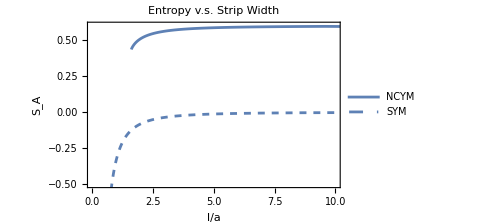

```mathematica
Show[{ListLinePlot[delsvsla07,PlotRange->{{0,10},{-0.5,0.6}},Frame->True,FrameLabel->{"l/a","S_A"},PlotLegends->{"NCYM"}],symdelspltt0},RotateLabel->False,PlotLabel->"Entropy v.s. Strip Width",ImageSize->Medium]
```

```mathematica
(*This is the holographic entanglement entropy for one strip of width l, calculated and plotted with dimensionless parameters*)
```

```mathematica
(*Now it's mutual information time*)
(*First need to define uc in terms of strip width, used interpolation function for this*)
```

```mathematica
ucvslinterp[a0_]:=Module[{a=a0,lvsuctb = {},ucvsltb={}},
For[i=0.001,i≤0.7991,i+=0.001,uc=i/a;
l=2*Quiet[NIntegrate[uc^3/(u^5 Sqrt[(1-(uc/u)^6)(1/(1+a^4 u^4))]),{u,uc,Infinity}]];
AppendTo[lvsuctb,{uc,l}];
AppendTo[ucvsltb,{l,uc}]
];
Clear[l];
Interpolation[ucvsltb]
]
```

```mathematica
(*Gonna plot a few of these to develop intuition. Above function adjusts Subscript[l, c] s.t. we see an accurate cutoff for each a value.*)
```

```mathematica
ucvsl0=ucvslinterp[0.01];
ucvsl05=ucvslinterp[0.5];
ucvsl1=ucvslinterp[1];
ucvsl12=ucvslinterp[1.2];
ucvsl20=ucvslinterp[2];
```

```mathematica
ucvsl0plt=Plot[ucvsl0[l],{l,0.25*1.6138741919546127,10},PlotRange->All,PlotStyle->Orange];
ucvsl05plt=Plot[ucvsl05[l],{l,0.5*1.6138741919546127,10},PlotRange->All,PlotStyle->Green];
ucvsl1plt=Plot[ucvsl1[l],{l,1.6138741919546127,10},PlotRange->All,PlotStyle->Black];
ucvsl12plt=Plot[ucvsl12[l],{l,1.2*1.6138741919546127,10},PlotRange->All,PlotStyle->Blue];
ucvsl20plt=Plot[ucvsl20[l],{l,2*1.6138741919546127,10},PlotRange->All,PlotStyle->Red];
```

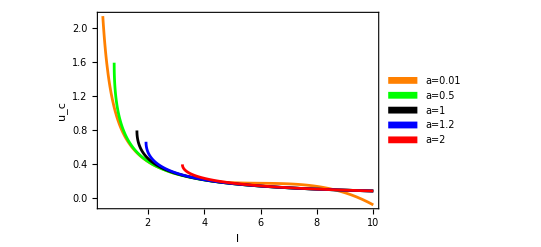

```mathematica
Legended[Show[{ucvsl0plt,ucvsl05plt,ucvsl1plt,ucvsl12plt,ucvsl20plt},Frame->True,FrameLabel->{"l","u_c"},RotateLabel->False],Placed[SwatchLegend[{Orange,Green,Black,Blue,Red},{"a=0.01","a=0.5","a=1","a=1.2","a=2"}],{0.8,0.7}]]
```

```mathematica
(*Now it's time to actually calculate mutual information, I made a silly lil guy to do that for me*)
```

```mathematica
mutinffunc[a0_,alpha_,lmult_]:=Module[{mutinfvsxtb={},a=a0},
firstucfunc=ucvslinterp[a];
lc=a*1.6138741919546127;
l=lc*lmult;
ucl=firstucfunc[l];
For[i=0.01,i≤1,i+=0.01,
x=lc+i*l;
ucx=firstucfunc[x];
uc2lx=firstucfunc[2l+x];
splint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(ucl/u)^6)],{u,ucl,alpha}]];
spxint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(ucx/u)^6)],{u,ucx,alpha}]];
sp2lxint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(uc2lx/u)^6)],{u,uc2lx,alpha}]];
mutinf=2*splint - sp2lxint - spxint;
AppendTo[mutinfvsxtb,{x,mutinf}];
];
mutinfvsxtb=Select[mutinfvsxtb,2.1>=#[[2]]>=-0.001&];
Return[mutinfvsxtb];
];
```

```mathematica
(*let's start with alpha=500, lmult = 4, and go through a few a values*)
```

```mathematica
mutinftb01=mutinffunc[0.1,500,4];
mutinftb05=mutinffunc[0.5,500,4];
mutinftb10=mutinffunc[1,500,4];
mutinftb12=mutinffunc[1.2,500,4];
mutinftb20=mutinffunc[2,500,4];
```

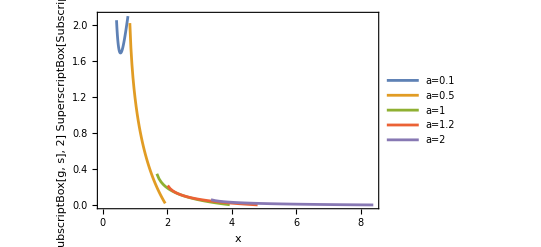

```mathematica
Show[ListLinePlot[{mutinftb01,mutinftb05,mutinftb10,mutinftb12,mutinftb20},PlotLegends->{"a=0.1","a=0.5","a=1","a=1.2","a=2"},Frame->True,FrameLabel->{"x","(2  SuperscriptBox[SubscriptBox[g, s], 2] SuperscriptBox[SubscriptBox[G, N], (5)])/L^2"Subscript[Style["Ι",FontFamily->"Times"], AB]}],RotateLabel->False]
```

```mathematica
(*ok so that's neat, but when a goes to zero there still be some issues. lets just ignore them for now and plot the whole guy versus x/l*)
```

```mathematica
(*mutinffuncxl[a0_,alpha_,lmult_]:=Module[{mutinfvsxltb={},a=a0},
firstucfunc=ucvslinterp[a];
lc=a*1.6138741919546127;
l=lc*lmult;
ucl=firstucfunc[l];
For[i=0,i≤1,i+=0.005,
x=lc+i*l;
ucx=firstucfunc[x];
uc2lx=firstucfunc[2l+x];
splint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(ucl/u)^6)],{u,ucl,alpha}]];
spxint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(ucx/u)^6)],{u,ucx,alpha}]];
sp2lxint=2*Quiet[NIntegrate[u*Sqrt[(1+(a*u)^4)/(1-(uc2lx/u)^6)],{u,uc2lx,alpha}]];
mutinf=2*splint - sp2lxint - spxint;
AppendTo[mutinfvsxltb,{x/l,mutinf}];
];
Return[mutinfvsxltb];
];*)
```

```mathematica
mutinffuncxl[a_,alpha_]:=Module[{mutinfvsxltb={}},
firstucfunc=ucvslinterp[a];
lc=1.6138741919546127;
l=2*lc;
ucl=firstucfunc[l];
splint=2*Quiet[NIntegrate[u*Sqrt[(1+a^4 u^4)/(1-(ucl/u)^6)],{u,ucl,alpha}]];
For[i=0,i≤1,i+=0.005,
x=i*l;
ucx=firstucfunc[x];
uc2lx=firstucfunc[2l+x];
spxint=2*Quiet[NIntegrate[u*Sqrt[(1+a^4 u^4)/(1-(ucx/u)^6)],{u,ucx,alpha}]];
sp2lxint=2*Quiet[NIntegrate[u*Sqrt[(1+a^4 u^4)/(1-(uc2lx/u)^6)],{u,uc2lx,alpha}]];
mutinf=1/a^2(2*splint - sp2lxint - spxint);
If[FreeQ[mutinf,Complex],AppendTo[mutinfvsxltb,{x/l,mutinf}]];
];
mutinfvsxltb=Select[mutinfvsxltb,2.1>=#[[2]]>=-0.005&];
Return[mutinfvsxltb];
];
```

```mathematica
(*mutinfxltb05=Quiet[mutinffuncxl[0.5,50]];*)
mutinfxltb10=Quiet[mutinffuncxl[1,30]];
mutinfxltb12=Quiet[mutinffuncxl[1.2,30]];
(*mutinfxltb20=Quiet[mutinffuncxl[2,30]];*)
```

```mathematica
(*Begin SYM code*)
```

```mathematica
symucvslinterp[uh_,ub_]:=Module[{ucvsltb={}},
For[uc=uh,uc<=3,uc+=0.01,
l=2*Quiet[NIntegrate[uc^3/Sqrt[(u^6-uc^6)(u^4-uh^4)],{u,uc,ub}]];
If[FreeQ[l,Complex],AppendTo[ucvsltb,{l,uc}]];
];
Clear[l];
Return[Interpolation[ucvsltb,InterpolationOrder->5]];
];
```

```mathematica
symmutinffuncxl[uh_,ub_,l_]:=Module[{mutinfvsxltb={}},
firstucfunc=symucvslinterp[uh,ub];
ucl=firstucfunc[l];
splint=2*Quiet[NIntegrate[u/Sqrt[(1-(ucl/u)^6)(1-(uh/u)^4)],{u,ucl,ub}]];
For[i=0,i<=1,i+=0.005,
x=i*l;
ucx=firstucfunc[x];
uc2lx=firstucfunc[2l+x];
spxint=2*Quiet[NIntegrate[u/Sqrt[(1-(ucx/u)^6)(1-(uh/u)^4)],{u,ucx,ub}]];
sp2lxint=2*Quiet[NIntegrate[u/Sqrt[(1-(uc2lx/u)^6)(1-(uh/u)^4)],{u,uc2lx,ub}]];
mutinf=2*splint-sp2lxint-spxint;
If[FreeQ[mutinf,Complex],AppendTo[mutinfvsxltb,{x/l,mutinf}]];
];
Return[mutinfvsxltb];
];
```

```mathematica
symmutinf0201=Quiet[symmutinffuncxl[0,200,2*1.6138741919546127]];
```

```mathematica
symmutinfpltt0=ListLinePlot[symmutinf0202,PlotRange->{{0.2,1},{0,1}},Frame->True,FrameLabel->{"x/l","(2  SuperscriptBox[SubscriptBox[g, s], 2] SuperscriptBox[SubscriptBox[G, N], (5)])/R^3"Subscript[Style["Ι",FontFamily->"Times"], AB]},PlotLegends->{"a=0"},PlotStyle->Dashed];
```

```mathematica
(*End SYM code*)
```

```mathematica
(*time to do a hacky thing, stole these gyus from temp notebook*)
```

```mathematica
mutinfvsxlnotemp1=Quiet[mutinffuncxl[1,0,ycmax0,lacrit0,7]];
mutinfvsxlnotemp2=Quiet[mutinffuncxl[1.1,0,ycmax0,lacrit0,7]];
```

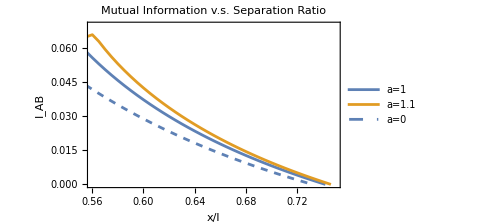

```mathematica
Show[{ListLinePlot[{(*mutinfxltb05,*)mutinfvsxlnotemp1,mutinfvsxlnotemp2(*,mutinfxltb20*)},FrameLabel->{"x/l",Subscript[Style["Ι",FontFamily->"Times"], AB]},PlotRange->{{0.56,0.75},{0,0.07}},Frame->True,PlotLabel->"Mutual Information v.s. Separation Ratio",PlotLegends->{(*"a=0.5",*)"a=1","a=1.1"(*,"a=2"*)}],symmutinfpltt0},RotateLabel->False,ImageSize->Medium]
```

```mathematica
(*to fix this: remove l dependence for the ncym plots, want everything to have same legnth and stuff*)
```

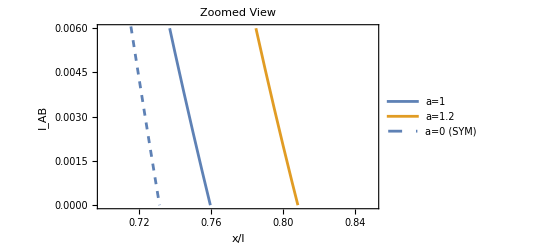

```mathematica
Show[{ListLinePlot[{(*mutinfxltb05,*)mutinfxltb10,mutinfxltb12(*,mutinfxltb20*)},PlotRange->{{0.7,0.85},{0,0.006}},Frame->True,PlotLabel->"Zoomed View",PlotLegends->{(*"a=0.5",*)"a=1","a=1.2"(*,"a=2"*)},FrameLabel->{"x/l",Subscript[Style["Ι",FontFamily->"Times"], AB]}],symmutinfpltt0},RotateLabel->False]
```